```mathematica
(*WALKING KINEMATICS: SINE WAVE SIGNIFICANCE TEST*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(*This code requires the data outputs from WALKING KINEMATICS: STICK FIGURE PLUS 3D JOINT ANGLES.nb and WALKING KINEMATICS: STICK FIGURE PLUS PELVIC VECTOR ANGLE ANALYSIS.nb. *)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Determine operating system *)

os=$OperatingSystem;
frogworkpath="C:\\YOUR FILE DIRECTORY HERE\\" (*Set your main file directory, not to the folder where raw or archived data are stored*)
(*e.g. frogworkpath="C:\\Users\\Documents\\"*)
(*for Mac users change "C:\\" to "\\Volumes\\*)
(***********************************************************************************)

(* Import metadata*)

(*SET DIRECTORY*)
dataDirectory="YOUR DIRECTORY TO METADATA.xlsx FILE";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

importedmetadata=Import["METADATA.xlsx","Data"];
metadata=importedmetadata[[1,2;;24,All]];

(***********************************************************************************)

(* Metadata file map: Locate information *)

Framerate=metadata[[1,3]]


(***********************************************************************************)

dataDirectory="YOUR DIRECTORY FOR PELVIC VECTOR ANGLE DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*IMPORT PELVIC ANGLE DATA*)

Animal0Trial1data=Import["KM01_RUN_02_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial1data=Import["KM02_RUN_01_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial2data=Import["KM02_RUN_02_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial3data=Import["KM02_RUN_09_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial1data=Import["KM04_RUN_09_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial2data=Import["KM04_RUN_11_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial3data=Import["KM04_RUN_12_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial1data=Import["KM05_RUN_04_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial2data=Import["KM05_RUN_08_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial1data=Import["KM06_RUN_11_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial2data=Import["KM06_RUN_12_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial3data=Import["KM06_RUN_13_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial4data=Import["KM06_RUN_15_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial5data=Import["KM06_RUN_16_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial1data=Import["KM07_RUN_14_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial2data=Import["KM07_RUN_16_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial3data=Import["KM07_RUN_17_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial1data=Import["KM08_RUN_09_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial2data=Import["KM08_RUN_10_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial1data=Import["KM23_RUN_01_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial2data=Import["KM23_RUN_02_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial3data=Import["KM23_RUN_03_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial4data=Import["KM23_RUN_05_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];



Animal0Trial1=Flatten[Animal0Trial1data[[1]]];
Animal1Trial1=Flatten[Animal1Trial1data[[1]]];
Animal1Trial2=Flatten[Animal1Trial2data[[1]]];
Animal1Trial3=Flatten[Animal1Trial3data[[1]]];
Animal2Trial1=Flatten[Animal2Trial1data[[1]]];
Animal2Trial2=Flatten[Animal2Trial2data[[1]]];
Animal2Trial3=Flatten[Animal2Trial3data[[1]]];
Animal3Trial1=Flatten[Animal3Trial1data[[1]]];
Animal3Trial2=Flatten[Animal3Trial2data[[1]]];
Animal4Trial1=Flatten[Animal4Trial1data[[1]]];
Animal4Trial2=Flatten[Animal4Trial2data[[1]]];
Animal4Trial3=Flatten[Animal4Trial3data[[1]]];
Animal4Trial4=Flatten[Animal4Trial4data[[1]]];
Animal4Trial5=Flatten[Animal4Trial5data[[1]]];
Animal5Trial1=Flatten[Animal5Trial1data[[1]]];
Animal5Trial2=Flatten[Animal5Trial2data[[1]]];
Animal5Trial3=Flatten[Animal5Trial3data[[1]]];
Animal6Trial1=Flatten[Animal6Trial1data[[1]]];
Animal6Trial2=Flatten[Animal6Trial2data[[1]]];
Animal7Trial1=Flatten[Animal7Trial1data[[1]]];
Animal7Trial2=Flatten[Animal7Trial2data[[1]]];
Animal7Trial3=Flatten[Animal7Trial3data[[1]]];
Animal7Trial4=Flatten[Animal7Trial4data[[1]]];
Dimensions[Animal1Trial1];
```

250.

```mathematica
(*********************************************************************)
(*********************************************************************)
```

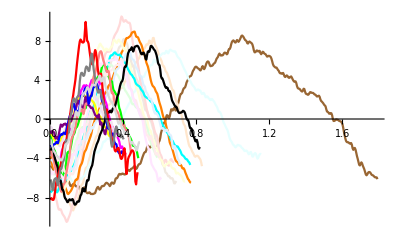

```mathematica
(*DEAL WITH OFFSET*)

(*1. Get average of all pelvic angles for each trial*)

AvAngleAnimal0Trial1=Mean[Animal0Trial1];
AvAngleAnimal1Trial1=Mean[Animal1Trial1];
AvAngleAnimal1Trial2=Mean[Animal1Trial2];
AvAngleAnimal1Trial3=Mean[Animal1Trial3];
AvAngleAnimal2Trial1=Mean[Animal2Trial1];
AvAngleAnimal2Trial2=Mean[Animal2Trial2];
AvAngleAnimal2Trial3=Mean[Animal2Trial3];
AvAngleAnimal3Trial1=Mean[Animal3Trial1];
AvAngleAnimal3Trial2=Mean[Animal3Trial2];
AvAngleAnimal4Trial1=Mean[Animal4Trial1];
AvAngleAnimal4Trial2=Mean[Animal4Trial2];
AvAngleAnimal4Trial3=Mean[Animal4Trial3];
AvAngleAnimal4Trial4=Mean[Animal4Trial4];
AvAngleAnimal4Trial5=Mean[Animal4Trial5];
AvAngleAnimal5Trial1=Mean[Animal5Trial1];
AvAngleAnimal5Trial2=Mean[Animal5Trial2];
AvAngleAnimal5Trial3=Mean[Animal5Trial3];
AvAngleAnimal6Trial1=Mean[Animal6Trial1];
AvAngleAnimal6Trial2=Mean[Animal6Trial2];
AvAngleAnimal7Trial1=Mean[Animal7Trial1];
AvAngleAnimal7Trial2=Mean[Animal7Trial2];
AvAngleAnimal7Trial3=Mean[Animal7Trial3];
AvAngleAnimal7Trial4=Mean[Animal7Trial4];
(*2. Find length of each trial (number of frames)*)

LengthAnimal0Trial1=Length[Animal0Trial1];
LengthAnimal1Trial1=Length[Animal1Trial1];
LengthAnimal1Trial2=Length[Animal1Trial2];
LengthAnimal1Trial3=Length[Animal1Trial3];
LengthAnimal2Trial1=Length[Animal2Trial1];
LengthAnimal2Trial2=Length[Animal2Trial2];
LengthAnimal2Trial3=Length[Animal2Trial3];
LengthAnimal3Trial1=Length[Animal3Trial1];
LengthAnimal3Trial2=Length[Animal3Trial2];
LengthAnimal4Trial1=Length[Animal4Trial1];
LengthAnimal4Trial2=Length[Animal4Trial2];
LengthAnimal4Trial3=Length[Animal4Trial3];
LengthAnimal4Trial4=Length[Animal4Trial4];
LengthAnimal4Trial5=Length[Animal4Trial5];
LengthAnimal5Trial1=Length[Animal5Trial1];
LengthAnimal5Trial2=Length[Animal5Trial2];
LengthAnimal5Trial3=Length[Animal5Trial3];
LengthAnimal6Trial1=Length[Animal6Trial1];
LengthAnimal6Trial2=Length[Animal6Trial2];
LengthAnimal7Trial1=Length[Animal7Trial1];
LengthAnimal7Trial2=Length[Animal7Trial2];
LengthAnimal7Trial3=Length[Animal7Trial3];
LengthAnimal7Trial4=Length[Animal7Trial4];

(*3.Make new data Tables of angle data corrected for offset - OC*)

OCAngleAnimal0Trial1=Table[Animal0Trial1[[i]]-AvAngleAnimal0Trial1,{i,1LengthAnimal0Trial1}];
OCAngleAnimal1Trial1=Table[Animal1Trial1[[i]]-AvAngleAnimal1Trial1,{i,1LengthAnimal1Trial1}];
OCAngleAnimal1Trial2=Table[Animal1Trial2[[i]]-AvAngleAnimal1Trial2,{i,1LengthAnimal1Trial2}];
OCAngleAnimal1Trial3=Table[Animal1Trial3[[i]]-AvAngleAnimal1Trial3,{i,1LengthAnimal1Trial3}];
OCAngleAnimal2Trial1=Table[Animal2Trial1[[i]]-AvAngleAnimal2Trial1,{i,1LengthAnimal2Trial1}];
OCAngleAnimal2Trial2=Table[Animal2Trial2[[i]]-AvAngleAnimal2Trial2,{i,1LengthAnimal2Trial2}];
OCAngleAnimal2Trial3=Table[Animal2Trial3[[i]]-AvAngleAnimal2Trial3,{i,1LengthAnimal2Trial3}];
OCAngleAnimal3Trial1=Table[Animal3Trial1[[i]]-AvAngleAnimal3Trial1,{i,1LengthAnimal3Trial1}];
OCAngleAnimal3Trial2=Table[Animal3Trial2[[i]]-AvAngleAnimal3Trial2,{i,1LengthAnimal3Trial2}];
OCAngleAnimal4Trial1=Table[Animal4Trial1[[i]]-AvAngleAnimal4Trial1,{i,1LengthAnimal4Trial1}];
OCAngleAnimal4Trial2=Table[Animal4Trial2[[i]]-AvAngleAnimal4Trial2,{i,1LengthAnimal4Trial2}];
OCAngleAnimal4Trial3=Table[Animal4Trial3[[i]]-AvAngleAnimal4Trial3,{i,1LengthAnimal4Trial3}];
OCAngleAnimal4Trial4=Table[Animal4Trial4[[i]]-AvAngleAnimal4Trial4,{i,1LengthAnimal4Trial4}];
OCAngleAnimal4Trial5=Table[Animal4Trial5[[i]]-AvAngleAnimal4Trial5,{i,1LengthAnimal4Trial5}];
OCAngleAnimal5Trial1=Table[Animal5Trial1[[i]]-AvAngleAnimal5Trial1,{i,1LengthAnimal5Trial1}];
OCAngleAnimal5Trial2=Table[Animal5Trial2[[i]]-AvAngleAnimal5Trial2,{i,1LengthAnimal5Trial2}];
OCAngleAnimal5Trial3=Table[Animal5Trial3[[i]]-AvAngleAnimal5Trial3,{i,1LengthAnimal5Trial3}];
OCAngleAnimal6Trial1=Table[Animal6Trial1[[i]]-AvAngleAnimal6Trial1,{i,1LengthAnimal6Trial1}];
OCAngleAnimal6Trial2=Table[Animal6Trial2[[i]]-AvAngleAnimal6Trial2,{i,1LengthAnimal6Trial2}];
OCAngleAnimal7Trial1=Table[Animal7Trial1[[i]]-AvAngleAnimal7Trial1,{i,1LengthAnimal7Trial1}];OCAngleAnimal7Trial2=Table[Animal7Trial2[[i]]-AvAngleAnimal7Trial2,{i,1LengthAnimal7Trial2}];OCAngleAnimal7Trial3=Table[Animal7Trial3[[i]]-AvAngleAnimal7Trial3,{i,1LengthAnimal7Trial3}];
OCAngleAnimal7Trial4=Table[Animal7Trial4[[i]]-AvAngleAnimal7Trial4,{i,1LengthAnimal7Trial4}];

(*4. Make xvalues in time*)
XValuesOneLimbCycleAnimal0Trial1=Table[x/Framerate,{x,1,LengthAnimal0Trial1}];
XValuesOneLimbCycleAnimal1Trial1=Table[x/Framerate,{x,1,LengthAnimal1Trial1}];
XValuesOneLimbCycleAnimal1Trial2=Table[x/Framerate,{x,1,LengthAnimal1Trial2}];
XValuesOneLimbCycleAnimal1Trial3=Table[x/Framerate,{x,1,LengthAnimal1Trial3}];
XValuesOneLimbCycleAnimal2Trial1=Table[x/Framerate,{x,1,LengthAnimal2Trial1}];
XValuesOneLimbCycleAnimal2Trial2=Table[x/Framerate,{x,1,LengthAnimal2Trial2}];
XValuesOneLimbCycleAnimal2Trial3=Table[x/Framerate,{x,1,LengthAnimal2Trial3}];
XValuesOneLimbCycleAnimal3Trial1=Table[x/Framerate,{x,1,LengthAnimal3Trial1}];
XValuesOneLimbCycleAnimal3Trial2=Table[x/Framerate,{x,1,LengthAnimal3Trial2}];
XValuesOneLimbCycleAnimal4Trial1=Table[x/Framerate,{x,1,LengthAnimal4Trial1}];
XValuesOneLimbCycleAnimal4Trial2=Table[x/Framerate,{x,1,LengthAnimal4Trial2}];
XValuesOneLimbCycleAnimal4Trial3=Table[x/Framerate,{x,1,LengthAnimal4Trial3}];
XValuesOneLimbCycleAnimal4Trial4=Table[x/Framerate,{x,1,LengthAnimal4Trial4}];
XValuesOneLimbCycleAnimal4Trial5=Table[x/Framerate,{x,1,LengthAnimal4Trial5}];
XValuesOneLimbCycleAnimal5Trial1=Table[x/Framerate,{x,1,LengthAnimal5Trial1}];
XValuesOneLimbCycleAnimal5Trial2=Table[x/Framerate,{x,1,LengthAnimal5Trial2}];
XValuesOneLimbCycleAnimal5Trial3=Table[x/Framerate,{x,1,LengthAnimal5Trial3}];
XValuesOneLimbCycleAnimal6Trial1=Table[x/Framerate,{x,1,LengthAnimal6Trial1}];
XValuesOneLimbCycleAnimal6Trial2=Table[x/Framerate,{x,1,LengthAnimal6Trial2}];
XValuesOneLimbCycleAnimal7Trial1=Table[x/Framerate,{x,1,LengthAnimal7Trial1}];
XValuesOneLimbCycleAnimal7Trial2=Table[x/Framerate,{x,1,LengthAnimal7Trial2}];XValuesOneLimbCycleAnimal7Trial3=Table[x/Framerate,{x,1,LengthAnimal7Trial3}];
XValuesOneLimbCycleAnimal7Trial4=Table[x/Framerate,{x,1,LengthAnimal7Trial4}];

(*5.Make new data Tables of time and angle data corrected for offset - OC*)

OCAnimal0Trial1=Thread[{XValuesOneLimbCycleAnimal0Trial1,OCAngleAnimal0Trial1}];
OCAnimal1Trial1=Thread[{XValuesOneLimbCycleAnimal1Trial1,OCAngleAnimal1Trial1}];
OCAnimal1Trial2=Thread[{XValuesOneLimbCycleAnimal1Trial2,OCAngleAnimal1Trial2}];
OCAnimal1Trial3=Thread[{XValuesOneLimbCycleAnimal1Trial3,OCAngleAnimal1Trial3}];
OCAnimal2Trial1=Thread[{XValuesOneLimbCycleAnimal2Trial1,OCAngleAnimal2Trial1}];
OCAnimal2Trial2=Thread[{XValuesOneLimbCycleAnimal2Trial2,OCAngleAnimal2Trial2}];
OCAnimal2Trial3=Thread[{XValuesOneLimbCycleAnimal2Trial3,OCAngleAnimal2Trial3}];
OCAnimal3Trial1=Thread[{XValuesOneLimbCycleAnimal3Trial1,OCAngleAnimal3Trial1}];
OCAnimal3Trial2=Thread[{XValuesOneLimbCycleAnimal3Trial2,OCAngleAnimal3Trial2}];
OCAnimal4Trial1=Thread[{XValuesOneLimbCycleAnimal4Trial1,OCAngleAnimal4Trial1}];
OCAnimal4Trial2=Thread[{XValuesOneLimbCycleAnimal4Trial2,OCAngleAnimal4Trial2}];
OCAnimal4Trial3=Thread[{XValuesOneLimbCycleAnimal4Trial3,OCAngleAnimal4Trial3}];
OCAnimal4Trial4=Thread[{XValuesOneLimbCycleAnimal4Trial4,OCAngleAnimal4Trial4}];
OCAnimal4Trial5=Thread[{XValuesOneLimbCycleAnimal4Trial5,OCAngleAnimal4Trial5}];
OCAnimal5Trial1=Thread[{XValuesOneLimbCycleAnimal5Trial1,OCAngleAnimal5Trial1}];
OCAnimal5Trial2=Thread[{XValuesOneLimbCycleAnimal5Trial2,OCAngleAnimal5Trial2}];
OCAnimal5Trial3=Thread[{XValuesOneLimbCycleAnimal5Trial3,OCAngleAnimal5Trial3}];
OCAnimal6Trial1=Thread[{XValuesOneLimbCycleAnimal6Trial1,OCAngleAnimal6Trial1}];
OCAnimal6Trial2=Thread[{XValuesOneLimbCycleAnimal6Trial2,OCAngleAnimal6Trial2}];
OCAnimal7Trial1=Thread[{XValuesOneLimbCycleAnimal7Trial1,OCAngleAnimal7Trial1}];
OCAnimal7Trial2=Thread[{XValuesOneLimbCycleAnimal7Trial2,OCAngleAnimal7Trial2}];
OCAnimal7Trial3=Thread[{XValuesOneLimbCycleAnimal7Trial3,OCAngleAnimal7Trial3}];
OCAnimal7Trial4=Thread[{XValuesOneLimbCycleAnimal7Trial4,OCAngleAnimal7Trial4}];

(*6. Make plots to check*)

OCAnimal0Trial1Plot=ListLinePlot[OCAnimal0Trial1,PlotStyle->Brown];
OCAnimal1Trial1Plot=ListLinePlot[OCAnimal1Trial1,PlotStyle->LightOrange];
OCAnimal1Trial2Plot=ListLinePlot[OCAnimal1Trial2,PlotStyle->LightCyan];
OCAnimal1Trial3Plot=ListLinePlot[OCAnimal1Trial3,PlotStyle->LightBrown];
OCAnimal2Trial1Plot=ListLinePlot[OCAnimal2Trial1,PlotStyle->LightRed];
OCAnimal2Trial2Plot=ListLinePlot[OCAnimal2Trial2,PlotStyle->Orange];
OCAnimal2Trial3Plot=ListLinePlot[OCAnimal2Trial3,PlotStyle->LightYellow];
OCAnimal3Trial1Plot=ListLinePlot[OCAnimal3Trial1,PlotStyle->Cyan];
OCAnimal3Trial2Plot=ListLinePlot[OCAnimal3Trial2,PlotStyle->LightGreen];
OCAnimal4Trial1Plot=ListLinePlot[OCAnimal4Trial1,PlotStyle->LightBlue];
OCAnimal4Trial2Plot=ListLinePlot[OCAnimal4Trial2,PlotStyle->Magenta];
OCAnimal4Trial3Plot=ListLinePlot[OCAnimal4Trial3,PlotStyle->Green];
OCAnimal4Trial4Plot=ListLinePlot[OCAnimal4Trial4,PlotStyle->LightPink];
OCAnimal4Trial5Plot=ListLinePlot[OCAnimal4Trial5,PlotStyle->LightMagenta];
OCAnimal5Trial1Plot=ListLinePlot[OCAnimal5Trial1,PlotStyle->LightPurple];
OCAnimal5Trial2Plot=ListLinePlot[OCAnimal5Trial2,PlotStyle->Yellow];
OCAnimal5Trial3Plot=ListLinePlot[OCAnimal5Trial3,PlotStyle->Purple];
OCAnimal6Trial1Plot=ListLinePlot[OCAnimal6Trial1,PlotStyle->Pink];
OCAnimal6Trial2Plot=ListLinePlot[OCAnimal6Trial2,PlotStyle->Black];
OCAnimal7Trial1Plot=ListLinePlot[OCAnimal7Trial1,PlotStyle->Blue];
OCAnimal7Trial2Plot=ListLinePlot[OCAnimal7Trial2,PlotStyle->Red];
OCAnimal7Trial3Plot=ListLinePlot[OCAnimal7Trial3,PlotStyle->Gray];
OCAnimal7Trial4Plot=ListLinePlot[OCAnimal7Trial4,PlotStyle->LightGray];

AllOCAnimal0Plot=Show[OCAnimal0Trial1Plot];
AllOCAnimal1Plot=Show[OCAnimal1Trial1Plot,OCAnimal1Trial2Plot,OCAnimal1Trial3Plot];
AllOCAnimal2Plot=Show[OCAnimal2Trial1Plot,OCAnimal2Trial2Plot,OCAnimal2Trial3Plot];
AllOCAnimal3Plot=Show[OCAnimal3Trial1Plot,OCAnimal3Trial2Plot];
AllOCAnimal4Plot=Show[OCAnimal4Trial1Plot,OCAnimal4Trial2Plot,OCAnimal4Trial3Plot,OCAnimal4Trial4Plot,OCAnimal4Trial5Plot];
AllOCAnimal5Plot=Show[OCAnimal5Trial1Plot,OCAnimal5Trial2Plot,OCAnimal5Trial3Plot];
AllOCAnimal6Plot=Show[OCAnimal6Trial1Plot,OCAnimal6Trial2Plot,PlotRange->All];
AllOCAnimal7Plot=Show[OCAnimal7Trial1Plot,OCAnimal7Trial2Plot,OCAnimal7Trial3Plot,OCAnimal7Trial4Plot,PlotRange->All];AllOCAnimalsAllTrials=Show[AllOCAnimal0Plot,AllOCAnimal1Plot,AllOCAnimal2Plot,AllOCAnimal3Plot,AllOCAnimal4Plot,AllOCAnimal5Plot,AllOCAnimal6Plot,AllOCAnimal7Plot,PlotRange->All]
```

```mathematica
(***************************************************************************)
```

```mathematica
(*STATISTICS*)

(*Combine all data*)
Alldata=Join[{OCAnimal0Trial1[[All,2]],OCAnimal1Trial1[[All,2]],OCAnimal1Trial2[[All,2]],OCAnimal1Trial3[[All,2]],OCAnimal2Trial1[[All,2]],OCAnimal2Trial2[[All,2]],OCAnimal2Trial3[[All,2]],OCAnimal3Trial1[[All,2]],OCAnimal3Trial2[[All,2]],OCAnimal4Trial1[[All,2]],OCAnimal4Trial2[[All,2]],OCAnimal4Trial3[[All,2]],OCAnimal4Trial4[[All,2]],OCAnimal4Trial5[[All,2]],OCAnimal5Trial1[[All,2]],OCAnimal5Trial2[[All,2]],OCAnimal5Trial3[[All,2]],OCAnimal6Trial1[[All,2]],OCAnimal6Trial2[[All,2]],OCAnimal7Trial1[[All,2]],OCAnimal7Trial2[[All,2]],OCAnimal7Trial3[[All,2]],OCAnimal7Trial4[[All,2]]}];
```

```mathematica
(*1. --- define necessary variables --- *)
data=Alldata[[23]]; (*CHANGE THIS PER TRIAL ---- 1-19 ---*)
n=Length[data];
seconds=data[[n]];
fs=250;
frequency=1/seconds;
```

```mathematica
(*2.----fourier transform the data and put it on logarithmic scale---*)
ftdataRaw=Fourier[data,FourierParameters->{1,-1}];
ftdata=ftdataRaw[[1;;Round[(n/2)]+1]];
psdata=(1/(fs*n))*(Abs@ftdata)^2;
psdata[[2;;Length[psdata]-1]]=2*psdata[[2;;Length[psdata]-1]];
logpsdata=10Log[10,psdata];
```

```mathematica
(*3. ---- Make frequency table and plot signal power against frequency ----- *)
(*------- then calculate fisher's g value which goes to significance test----*)
frequencytable=Table[i,{i,0,fs/2,fs/n}];
Max[logpsdata]/Total[logpsdata];
fisherg=Max[psdata]/Total[psdata];
ListLinePlot[data]
thread=Thread[{N@frequencytable,logpsdata}];
ListLinePlot[thread]
Length[frequencytable]
Length[logpsdata]
```

62

63

```mathematica
(*calculate the p-value using g statistic plugged into some kind of cumulative probability function*)
n=Length[logpsdata];
g=fisherg;
k=Floor[1/g];
term1=n*(1-g)^(n-1);
term2=-(n*(n-1))/2*(1-2*g)^(n-1);
pvalue=Sum[
If[i==1,term1,If[i==2,term1+term2,term1+term2-1^(i-1)*Binomial[n,i]*(1-i*g)^(n-1)]]
,{i,1,k}] (*THE OUTPUT IS YOUR P VALUE AND IT SHOULD BE AN EXTREMELY SMALL NUMBER*)
```

1.60966×10^-85